```mathematica
;;;
```

Last updated:   Tue 11 Jul 2023
Author:   Martins Dogo

# Some interesting cellular automata

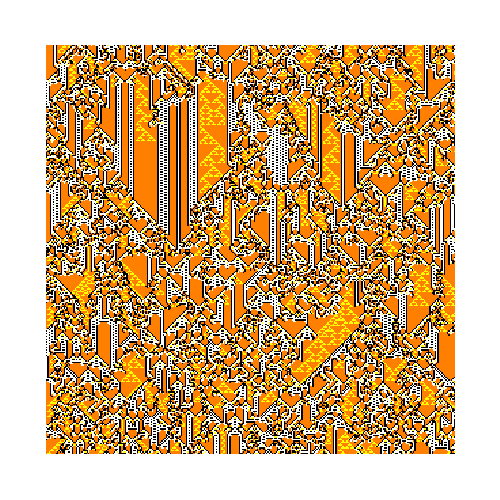

```mathematica
ArrayPlot[CellularAutomaton[{1170144720,{5,1}},{{1},0},{{500,800},{0,300}}],
ImageSize->500,ColorRules->{0->Black,1->White,2->Black,3->Yellow,4->Orange}]
```

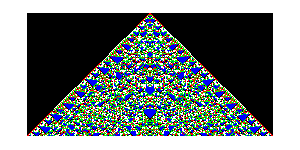
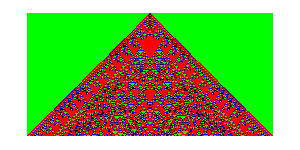
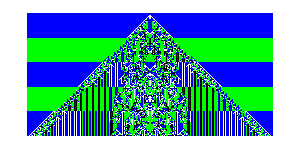
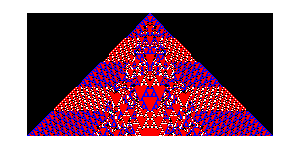
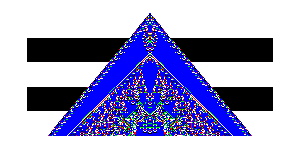
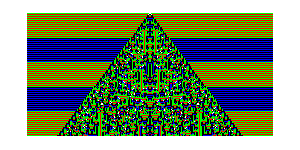
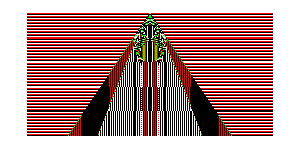
-Graphics-1121354535 | -Graphics-866055878 | -Graphics-898015754 | -Graphics-504017495 | -Graphics-1131608171
-Graphics-565480033 | -Graphics-381736257 | -Graphics-337288754 | -Graphics-1114078045 | -Graphics-523277670
-Graphics-838634019 | -Graphics-669253208 | -Graphics-754687672 | -Graphics-1170144720 | -Graphics-684598140
-Graphics-432501717 | -Graphics-1183118715 | -Graphics-661285711 | -Graphics-235853254 | -Graphics-1045884213
-Graphics-108650044 | -Graphics-426343194 | -Graphics-980418173 | -Graphics-1043092467 | -Graphics-544659819
-Graphics-121011884 | -Graphics-428119715 | -Graphics-892834877 | -Graphics-1068235705 | -Graphics-1205463761
-Graphics-460872323 | -Graphics-919480578 | -Graphics-380575390 | -Graphics-1119821761 | 
-Graphics-585864084 | -Graphics-638917829 | -Graphics-413595892 | -Graphics-1063296777 |

```mathematica
ParallelTable[
Labeled[ArrayPlot[CellularAutomaton[{i,{5,1}},{{1},0},{250,All}],
ImageSize->300,PlotRangePadding->None,ColorRules->{0->Black,1->White,2->Red,3->Green,4->Blue(*2->Pink,3->Yellow,4->Purple*)}
],i,Bottom],{i,
{1121354535,565480033,838634019,432501717,108650044,121011884,460872323,585864084,866055878,381736257,669253208,1183118715,426343194,428119715,919480578,638917829,898015754,337288754,754687672,661285711,980418173,892834877,380575390,413595892,504017495,1114078045,1170144720,235853254,1043092467,1068235705,1119821761,1063296777,1131608171,523277670,684598140,1045884213,544659819,1205463761}
}]//Multicolumn[#,5]&
```

```mathematica
ParallelTable[
ArrayPlot[CellularAutomaton[{i,{5,1}},{{1},0},{250,All}],
ImageSize->500,ColorRules->{0->Black,1->White,2->Pink,3->Yellow,4->Orange}
],{i,{261595317,73355063}}]//Multicolumn[#,3]&
```

-Graphics- | -Graphics- |

```mathematica
ParallelTable[
ArrayPlot[CellularAutomaton[{i,{5,1}},{{1},0},{500,All}],
ImageSize->500,ColorRules->{0->Black,1->White,2->Pink,3->Yellow,4->Orange}
],{i,{598736632,1067328686,1052966286}}](*//Multicolumn[#,3]&*)
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[
ArrayPlot[CellularAutomaton[{i,{5,1}},{{1},0},{500,All}],
ImageSize->500,ColorRules->{0->Black,1->White,2->Pink,3->Yellow,4->Orange}
],{i,{1141146023,787568853,1200590355}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[
ArrayPlot[CellularAutomaton[{i,{5,1}},{{1},0},{500,All}],
ImageSize->500,ColorRules->{0->Black,1->White,2->Pink,3->Yellow,4->Orange}
],{i,{323925770,620000441,1053060147,1043923764}}]//Multicolumn[#,3]&
```

-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
ParallelTable[
ArrayPlot[CellularAutomaton[{i,{5,1}},{{1},0},{500,All}],
ImageSize->500,ColorRules->{0->Black,1->White,2->Pink,3->Yellow,4->Orange}
],{i,{563164536,253842871,1214435255,1183307273}}]//Multicolumn[#,3]&
```

-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |